General::ivar: a+ⅈ b is not a valid variable.

0.0183156 (a+ⅈ b) ⅇ^(4. √(1+0.625 (a+ⅈ b)))

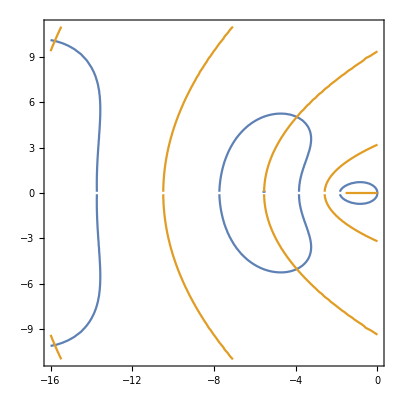

-3.94784+5.02655 ⅈ

-15.7914+10.0531 ⅈ

```mathematica
param={μ->0.8,vt->1,d->0.1};

P[x_]=vt*Exp[-(μ*x-vt)^2/(4*vt*x)]/Sqrt[4*d*Pi*x^3]/.param;

s=a+I*b;

PL=Exp[(μ*vt/(2*d))*(1-Sqrt[1+4*d*s/μ^2])]/.param;

Finv=s/(PL);
g=Normal[Simplify[Series[Finv,{s,0,1}]]]

(*PL=Exp[(μ*vt/(2*d))*(1-Sqrt[1+4*d*[a+I*b]/μ^2])]/.param;*)


(*Plot3D[{Re[(PL-1)],Im[(PL-1)],0},{a,-16,0},{b,-11,11}]*)

ContourPlot[{Re[PL]==1,Im[PL]==0},{a,-16,0},{b,-11,11}]

l[n_]=-2*Pi*μ*n/vt*(2*Pi*n*d/(vt*μ) -I)/.param;
l1=l[1]
l2=l[2]


(*Integrate[Integrate[v*Exp[-l*x]*Exp[-(μ*x-vt)^2/(4*vt*x)]/Sqrt[4*d*Pi*x^3],{x,t,Infinity}],{t,0,Infinity}]*)
```

```mathematica
Reduce[PL==1 && -16<a<0 &&-11<b<11,{a,b}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(a==-15.7914&&(b==-10.0531||b==10.0531))||(a==-3.94784&&(b==-5.02655||b==5.02655))

Resolve::bddom: Value {b,-11,11} of the domain argument should be Complexes, Reals, Algebraics, Rationals, Integers, Primes, Booleans, or Automatic.

```mathematica
M[i_]=Integrate[P[x]x^i,{x,0,Infinity}];



F[eig_]=Sum[(-1)^n*eig^n*M[n]/Factorial[n],{n,1,300}];
```

```mathematica
Resolve[F[x]==0]
```

-3.95285 x+8.64685 x^2-28.0508 x^3+110.699 x^4-486.501 x^5+2286.24 x^6-11245.2 x^7+57168.2 x^8-297995. x^9+1.58409×10^6 x^10-8.55472×10^6 x^11+4.68024×10^7 x^12-2.58849×10^8 x^13+1.44487×10^9 x^14-8.12932×10^9 x^15+4.60544×10^10 x^16-2.62489×10^11 x^17+1.50408×10^12 x^18-8.65955×10^12 x^19+5.00692×10^13 x^20-2.90612×10^14 x^21+1.69266×10^15 x^22-9.89006×10^15 x^23+5.79543×10^16 x^24-3.40507×10^17 x^25+2.00553×10^18 x^26-1.1839×10^19 x^27+7.00338×10^19 x^28-4.15094×10^20 x^29+2.46474×10^21 x^30-1.466×10^22 x^31+8.73337×10^22 x^32-5.21047×10^23 x^33+3.11299×10^24 x^34-1.8623×10^25 x^35+1.11548×10^26 x^36-6.68934×10^26 x^37+4.01593×10^27 x^38-2.41349×10^28 x^39+1.4519×10^29 x^40-8.74264×10^29 x^41+5.26914×10^30 x^42-3.17841×10^31 x^43+1.91883×10^32 x^44-1.15932×10^33 x^45+7.00959×10^33 x^46-4.24126×10^34 x^47+2.568×10^35 x^48-1.5559×10^36 x^49+9.43278×10^36 x^50-5.72219×10^37 x^51+3.47326×10^38 x^52-2.10938×10^39 x^53+1.28176×10^40 x^54-7.79263×10^40 x^55+4.74×10^41 x^56-2.88458×10^42 x^57+1.75626×10^43 x^58-1.06977×10^44 x^59+6.51898×10^44 x^60-3.97422×10^45 x^61+2.42382×10^46 x^62-1.47883×10^47 x^63+9.02618×10^47 x^64-5.51123×10^48 x^65+3.36627×10^49 x^66-2.05684×10^50 x^67+1.25718×10^51 x^68-7.68661×10^51 x^69+4.70123×10^52 x^70-2.87621×10^53 x^71+1.7602×10^54 x^72-1.07753×10^55 x^73+6.59808×10^55 x^74-4.04136×10^56 x^75+2.47601×10^57 x^76-1.51737×10^58 x^77+9.30127×10^58 x^78-5.70295×10^59 x^79+3.49754×10^60 x^80-2.14549×10^61 x^81+1.31641×10^62 x^82-8.07893×10^62 x^83+4.9592×10^63 x^84-3.04482×10^64 x^85+1.86983×10^65 x^86-1.1485×10^66 x^87+7.05582×10^66 x^88-4.33558×10^67 x^89+2.66459×10^68 x^90-1.63793×10^69 x^91+1.00702×10^70 x^92-6.19238×10^70 x^93+3.8085×10^71 x^94-2.34274×10^72 x^95+1.44134×10^73 x^96-8.8691×10^73 x^97+5.45837×10^74 x^98-3.35981×10^75 x^99+2.06839×10^76 x^100-1.27355×10^77 x^101+7.84266×10^77 x^102-4.8303×10^78 x^103+2.97541×10^79 x^104-1.83307×10^80 x^105+1.12946×10^81 x^106-6.96019×10^81 x^107+4.28972×10^82 x^108-2.64419×10^83 x^109+1.63009×10^84 x^110-1.00504×10^85 x^111+6.19739×10^85 x^112-3.82197×10^86 x^113+2.35731×10^87 x^114-1.4541×10^88 x^115+8.97066×10^88 x^116-5.5348×10^89 x^117+3.41528×10^90 x^118-2.10765×10^91 x^119+1.30082×10^92 x^120-8.02936×10^92 x^121+4.95667×10^93 x^122-3.06015×10^94 x^123+1.88946×10^95 x^124-1.16674×10^96 x^125+7.20536×10^96 x^126-4.45017197383379×10^97 x^127+2.74877037630785×10^98 x^128-1.69800916741019×10^99 x^129+1.049013032306×10^100 x^130-6.48127453358069×10^100 x^131+4.00477428298081×10^101 x^132-2.47476055322412×10^102 x^133+1.52941476716099×10^103 x^134-9.45265431134494×10^103 x^135+5.8427612000251×10^104 x^136-3.6117512783927×10^105 x^137+2.23281302399412×10^106 x^138-1.3804516416455×10^107 x^139+8.53539973004369×10^107 x^140-5.27788443011219×10^108 x^141+3.2638392420753×10^109 x^142-2.01850604002911×10^110 x^143+1.24842743622141×10^111 x^144-7.72196929020906×10^111 x^145+4.77665545760404×10^112 x^146-2.95495191894729×10^113 x^147+1.82813035676583×10^114 x^148-1.13108106866713×10^115 x^149+6.99857689293122×10^115 x^150-4.33066693140868×10^116 x^151+2.67996106859288×10^117 x^152-1.65855724743696×10^118 x^153+1.02650332035824×10^119 x^154-6.3535697145684×10^119 x^155+3.93280519451656×10^120 x^156-2.43452319246657×10^121 x^157+1.50713412129701×10^122 x^158-9.33073935981307×10^122 x^159+5.77704905561761×10^123 x^160-3.5770216704155×10^124 x^161+2.21494164798994×10^125 x^162-1.37160133496891×10^126 x^163+8.49411420150253×10^126 x^164-5.26056728333847×10^127 x^165+3.258149868585×10^128 x^166-2.01805612090167×10^129 x^167+1.2500254162095×10^130 x^168-7.7433268314002×10^130 x^169+4.79688389794473×10^131 x^170-2.97175789263949×10^132 x^171+1.84115342294276×10^133 x^172-1.14074510107022×10^134 x^173+7.06820387921143×10^134 x^174-4.37976790015987×10^135 x^175+2.71402879375466×10^136 x^176-1.6818950403604×10^137 x^177+1.04232745070579×10^138 x^178-6.45996364251019×10^138 x^179+4.00383668733564×10^139 x^180-2.48166292332154×10^140 x^181+1.53825793501255×10^141 x^182-9.53531953867977×10^141 x^183+5.91099836023887×10^142 x^184-3.66442396845794×10^143 x^185+2.27179778549749×10^144 x^186-1.40848590153705×10^145 x^187+8.73280998513768×10^145 x^188-5.41469492460283×10^146 x^189+3.35747088296457×10^147 x^190-2.08194190046349×10^148 x^191+1.29104938638618×10^149 x^192-8.00635455243323×10^149 x^193+4.9652864809509×10^150 x^194-3.07943578785487×10^151 x^195+1.90991995316634×10^152 x^196-1.18461213080329×10^153 x^197+7.34774387873972×10^153 x^198-4.55772899426344×10^154 x^199+2.82721915138967×10^155 x^200-1.75382708463421×10^156 x^201+1.08800334812294×10^157 x^202-6.74978114854002×10^157 x^203+4.18759810810341×10^158 x^204-2.59810073834788×10^159 x^205+1.61199063008142×10^160 x^206-1.00019441360272×10^161 x^207+6.20614005690564×10^161 x^208-3.85100258362642×10^162 x^209+2.38968684835523×10^163 x^210-1.48293795374144×10^164 x^211+9.2027925236092×10^164 x^212-5.71124520977386×10^165 x^213+3.54451135285313×10^166 x^214-2.19986581696422×10^167 x^215+1.36536929945401×10^168 x^216-8.47457772599189×10^168 x^217+5.2601710168674×10^169 x^218-3.26509180372118×10^170 x^219+2.0267703397421×10^171 x^220-1.25813478678324×10^172 x^221+7.8102181801342×10^172 x^222-4.84855589607112×10^173 x^223+3.01005737293756×10^174 x^224-1.86874545551393×10^175 x^225+1.1602148484892×10^176 x^226-7.20343213254253×10^176 x^227+4.47252920995217×10^177 x^228-2.77702288513682×10^178 x^229+1.72432124326398×10^179 x^230-1.07070353674079×10^180 x^231+6.6486355558622×10^180 x^232-4.1286488330404×10^181 x^233+2.56386636499683×10^182 x^234-1.59218946096202×10^183 x^235+9.88794230263066×10^183 x^236-6.14085469122072×10^184 x^237+3.81384763000417×10^185 x^238-2.36869627922006×10^186 x^239+1.47118349357298×10^187 x^240-9.1376735853196×10^187 x^241+5.6756508868629×10^188 x^242-3.52538743094633×10^189 x^243+2.18982335020283×10^190 x^244-1.36026108924009×10^191 x^245+8.44979826652857×10^191 x^246-5.24905581177108×10^192 x^247+3.26081933680522×10^193 x^248-2.02573623242465×10^194 x^249+1.25848945287256×10^195 x^250-7.81855879146731×10^195 x^251+4.85751545321952×10^196 x^252-3.01794938768624×10^197 x^253+1.87508046353942×10^198 x^254-1.16503233958212×10^199 x^255+7.23879185193034×10^199 x^256-4.49784157562037×10^200 x^257+2.79480878950885×10^201 x^258-1.7366402006175×10^202 x^259+1.07913885006926×10^203 x^260-6.70585964026839×10^203 x^261+4.16716953708926×10^204 x^262-2.58962802714102×10^205 x^263+1.60932233248886×10^206 x^264-1.00013367886967×10^207 x^265+6.21558998787339×10^207 x^266-3.86292153969018×10^208 x^267+2.40081430109961×10^209 x^268-1.49214262521214×10^210 x^269+9.27408606466351×10^210 x^270-5.76422411448422×10^211 x^271+3.5827745370197×10^212 x^272-2.22693181456242×10^213 x^273+1.38421361213769×10^214 x^274-8.60415059333791×10^214 x^275+5.348370915415×10^215 x^276-3.3246321447615×10^216 x^277+2.06668451153667×10^217 x^278-1.28473398505632×10^218 x^279+7.98657589341446×10^218 x^280-4.96496688010065×10^219 x^281+3.08660000092573×10^220 x^282-1.91890092848328×10^221 x^283+1.19297928029131×10^222 x^284-7.41688146666498×10^222 x^285+4.61124087355603×10^223 x^286-2.86696410655278×10^224 x^287+1.78252087283725×10^225 x^288-1.10829368470832×10^226 x^289+6.89101039300985×10^226 x^290-4.28468312758149×10^227 x^291+2.66417174780313×10^228 x^292-1.65658368456468×10^229 x^293+1.03008281261389×10^230 x^294-6.40528488068087×10^230 x^295+3.98301788494943×10^231 x^296-2.47681465906872×10^232 x^297+1.54021787266095×10^233 x^298-9.57807326302457×10^233 x^299+5.95636699337587×10^234 x^300==0